# Project Euler problem 108

### Brute force

```mathematica
n=4;
```

```mathematica
DiophantineReciprocal[x,y,n]
```

-1/4+1/x+1/y

```mathematica
sol[n_]:=Cases[
Table[
Flatten[{x,-(n x)/(n-x)}],
{x,n+1,2n}
],
{_Integer,_Integer}
]
```

```mathematica
n=1;
While[
Length[sol[n]]≤ 100,
n++
];
n
```

1260

```mathematica
list=Table[{n,Length[sol[n]]},{n,1,1260}];
```

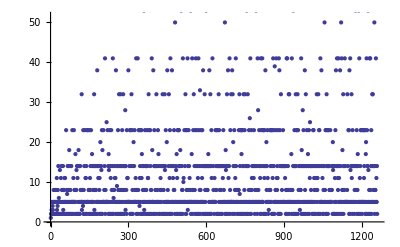

```mathematica
ListPlot[list]
```

```mathematica
n=1;
While[
Length[sol[n]]≤ 1000,
n++
]//AbsoluteTiming
n
```

$Aborted

14400

### With a little intelligence

```mathematica
DiophantineReciprocal[xx,yy,nn]
```

-1/nn+1/xx+1/yy

```mathematica
Clear[x,y,n];
Solve[DiophantineReciprocal[x,y,n]==0,x]
```

{{x→-(n y)/(n-y)}}

x= -(n y)/(n-y)=(n (n-y-n))/(n-y)=n+n^2/(y-n)
x is between [n+1, 2n], so n^2/(y-n) is between [1, n], the number of solutions is equale to the number of different possible values of n^2/(y-n), which is a divisor of n^2.

```mathematica
n=1;
ClearSystemCache[]
While[Length[Select[Divisors[n^2],#≤ n&]]≤1000,n++]//AbsoluteTiming
n
```

{18.48523,Null}

180180

```mathematica
With[{n=180180},Length[Select[Divisors[n^2],#≤ n&]]]
With[{n=180180-1},Length[Select[Divisors[n^2],#≤ n&]]]
```

1013

2

Here we can reconstruct all pairs of x and y which satisfy the original Diophantine reciprocal equation.

```mathematica
solutions[n_]:=Table[{n+d,n^2/d+n},{d,Select[Divisors[n^2],#≤  n&]}]
```

```mathematica
solutions[4]
```

{{5,20},{6,12},{8,8}}

```mathematica
solutions[1000]
```

{{1001,1001000},{1002,501000},{1004,251000},{1005,201000},{1008,126000},{1010,101000},{1016,63500},{1020,51000},{1025,41000},{1032,32250},{1040,26000},{1050,21000},{1064,16625},{1080,13500},{1100,11000},{1125,9000},{1160,7250},{1200,6000},{1250,5000},{1320,4125},{1400,3500},{1500,3000},{1625,2600},{1800,2250},{2000,2000}}

### One-liner

```mathematica
Module[{n=1},While[Length[Select[Divisors[n^2],#≤ n&]]≤1000,n++];n]
```

### WolframAlpha

http://www.wolframalpha.com/input/?i=1%2Fa%2B1%2Fb%3D1%2F10+integer+solutions

#### One-liner solution

```mathematica
n=5;
$query="1/a+1/b=1/"<>ToString[n]<>" integer solutions"
```

1/a+1/b=1/5 integer solutions

```mathematica
Composition[
DeleteDuplicates,
Sort/@#&,
Cases[#,_[lhs_,Verbatim[Hold][And[Equal[_,avalue_?(#>0&)],Equal[_,bvalue_?(#>0&)]]]]:> {avalue,bvalue}]&,
WolframAlpha[#,{"Result","ComputableData"},TimeConstraint-> 100]&
][$query]
```

{{6,30},{10,10}}

#### Details

```mathematica
?WolframAlpha
```

WolframAlpha[query] sends query to Wolfram|Alpha and imports the output.
WolframAlpha[query,format] imports the output according to the specified format.

```mathematica
$query="1/a+1/b=1/4 integer solutions";
```

```mathematica
WolframAlpha[$query,"PodIDs"]
```

{Input,Result,ImplicitPlot}

```mathematica
Options[WolframAlpha]//InputForm
```

{AppearanceElements -> Automatic, Asynchronous -> False, ExcludePods -> None, IgnoreCase -> False, IncludePods -> All, InputAssumptions -> {}, Method -> {}, 
 PodStates -> {}, PodWidth -> Automatic, TimeConstraint -> 30}

```mathematica
WolframAlpha[$query,TimeConstraint-> 100]
```

WolframAlphaQueryResults

```mathematica
WolframAlpha[$query,{{"Result",1}},TimeConstraint-> 100,Asynchronous-> True]
```

{{{Result,1},Plaintext},{{Result,1},Input},{{Result,1},Output},{{Result,1},Cell},{{Result,1},Content},{{Result,1},Image},{{Result,1},DataFormats},{{Result,1},ComputableData},{{Result,1},FormattedData},{{Result,1},FormulaData}}

```mathematica
WolframAlpha[$query,{{"Result",1},"ComputableData"},TimeConstraint-> 100,Asynchronous-> True]
```

Hold[a==-12&&b==3]

```mathematica
WolframAlpha[$query,"Result",TimeConstraint-> 100]
```

-4+a≠0&&b==(4 a)/(-4+a)&&a≠0

```mathematica
WolframAlpha[$query,{"Result","ComputableData"},TimeConstraint-> 100]
```

{{{Result,1},ComputableData}→Hold[a==-12&&b==3],{{Result,2},ComputableData}→Hold[a==-4&&b==2],{{Result,3},ComputableData}→Hold[a==2&&b==-4],{{Result,4},ComputableData}→Hold[a==3&&b==-12],{{Result,5},ComputableData}→Hold[a==5&&b==20],{{Result,6},ComputableData}→Hold[a==6&&b==12],{{Result,7},ComputableData}→Hold[a==8&&b==8],{{Result,8},ComputableData}→Hold[a==12&&b==6],{{Result,9},ComputableData}→Hold[a==20&&b==5]}